# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Liu Scattering

```mathematica
pLiu[u_,e_,m_]:=(e(2m+1)(1+e u)^(2m))/(2 Pi((1+e)^(2m+1)-(1-e)^(2m+1)))
```

```mathematica
Clear[m]
```

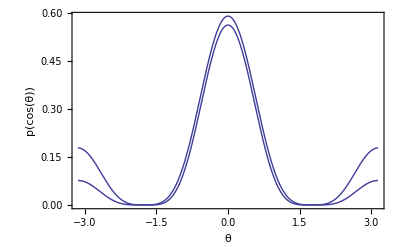

```mathematica
pLiuplot=Show[
Plot[pLiu[Cos[t],4,2],{t,-Pi,Pi},PlotRange->All],
Plot[pLiu[Cos[t],7,2],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Liu Scattering, (m = 2, ϵ = 4), (m = 2, ϵ = 7)"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers&&e<1]
```

((1+e)^(1+2 m) (-1+e+2 e m)+(1-e)^(1+2 m) (1+e+2 e m))/(2 e (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

1

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

(5 ((1+e)^(1+2 m) (3+e (-3+2 m (-3+2 e (1+m))))+(1-e)^(2 m) (-1+e) (3+e (3+2 m (3+2 e (1+m))))))/(2 e^2 (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m) (3+2 m))

### sampling

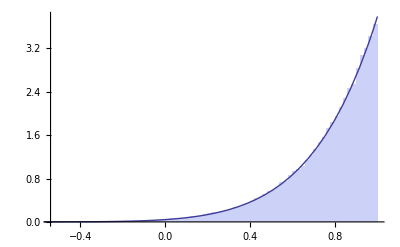

```mathematica
m=3.5;
ϵ=0.9;
Show[Histogram[Map[(-1+((-1+#) (1-ϵ)^(2 m) (-1+ϵ)+# (1+ϵ)^(1+2 m))^(1/(1+2 m)))/ϵ&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pLiu[u,ϵ,m],{u,-1,1},PlotRange->All]

]
Clear[m,ϵ];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pLiu[(-1+((-1+#) (1-ϵ)^(2 m) (-1+ϵ)+# (1+ϵ)^(1+2 m))^(1/(1+2 m)))/ϵ&[ξ],ϵ,m],Assumptions->ϵ>0&&m>0&&0<ξ<1]
```

((1+2 m) ϵ ((1-ϵ)^(2 m) (-1+ϵ) (-1+ξ)+(1+ϵ)^(1+2 m) ξ)^((2 m)/(1+2 m)))/(2 π (-(1-ϵ)^(1+2 m)+(1+ϵ)^(1+2 m)))